```mathematica
time={0,1,2,3,4,5,6,7,8,9,10,11,12};
s={762,750,740,721,613,332,264,119,99,78,68,30,22};
i={1,12,15,29,124,128,270,252,232,204,150,96,62};
rmv={0,1,8,13,26,113,161,247,412,481,545,637,679};
r=0.44036;
error[a_]:=(
result=NDSolve[{S'[t]==-a S[t] Inf[t],Inf'[t]==a S[t] Inf[t]-r Inf[t], R'[t]==r  Inf[t],S[0]==762,Inf[0]==1,R[0]==0},{S,Inf,R},{t,0,12}][[1]];
Susp[t_]=S[t]/.result;
Infect[t_]=Inf[t]/.result;
Rmv[t_]=R[t]/.result;
Join[Susp[time]-s,Infect[time]-i,Rmv[time]-rmv]
);
```

```mathematica
h=0.0001;
old=2;
new=1;
allNew={};
While[old-new>0.000001,
old=new;
α=1;
new=old-α*Norm[((error[old+h]-error[old])/h)];
While[Norm[error[new]]-Norm[error[old]]>0,
α=α/2;
new=old-α*Norm[((error[old+h]-error[old])/h)];
];
AppendTo[allNew,new];
];
new
```

0.00176725

```mathematica
allNew
```

{0.126048,0.0146776,0.00427557,0.00268074,0.00176725,0.00176725}

{S→InterpolatingFunction[{{0., 14.}}, <>],Inf→InterpolatingFunction[{{0., 14.}}, <>],R→InterpolatingFunction[{{0., 14.}}, <>]}

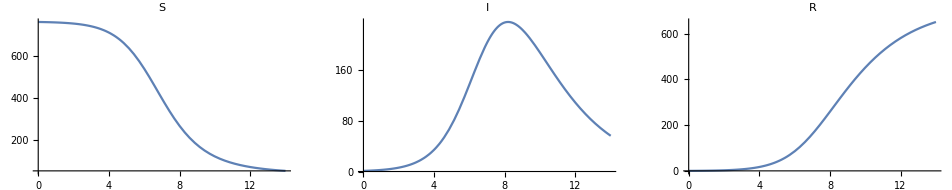

```mathematica
a=0.0017672509921504462;
r=0.44036;
result=NDSolve[{S'[t]==-a S[t] Inf[t],Inf'[t]==a S[t] Inf[t]-r Inf[t], R'[t]==r Inf[t],S[0]==762,Inf[0]==1,R[0]==0},{S,Inf,R},{t,0,14}][[1]]
S[t_]=S[t]/.result;
Inf[t_]=Inf[t]/.result;
R[t_]=R[t]/.result;
GraphicsRow[{Plot[S[t],{t,0,14},PlotRange->All,PlotLabel ->"S"],Plot[Inf[t],{t,0,14},PlotRange->All,PlotLabel->"I"],Plot[R[t],{t,0,14},PlotRange->All,PlotLabel ->"R"]}]
```

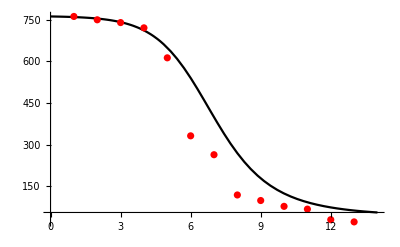

```mathematica
gr1=ListPlot[s,PlotStyle -> Red];
gr2=Plot[S[t],{t,0,14},PlotRange->All,PlotStyle -> Black];
Show[gr2,gr1]
```

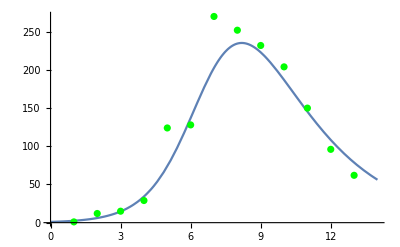

```mathematica
gr3 = ListPlot[i,PlotStyle-> Green];
gr4=Plot[Inf[t],{t,0,14},PlotRange->All];
Show[gr4,gr3]
```

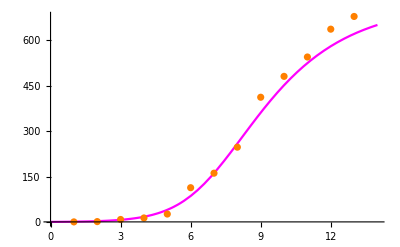

```mathematica
gr5 = ListPlot[rmv,PlotStyle-> Orange];
gr6=Plot[R[t],{t,0,14},PlotRange->All,PlotStyle -> Magenta];
Show[gr6,gr5]
```

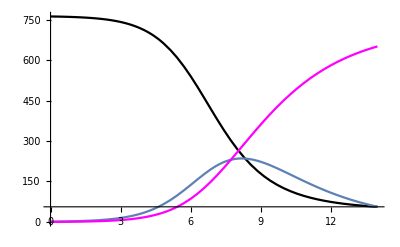

```mathematica
Show[gr2,gr4,gr6]
```

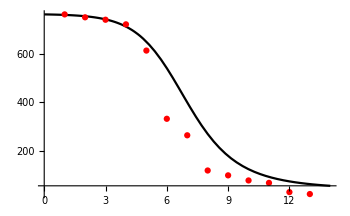
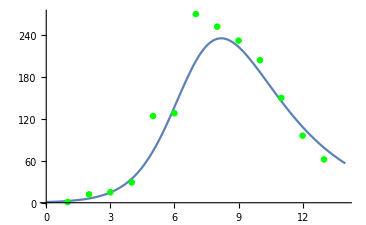
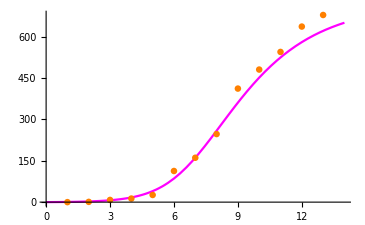
GraphicsRow[-Graphics-,-Graphics-,-Graphics-]

```mathematica
GraphicsRow[Show[gr2,gr1],Show[gr4,gr3],Show[gr6,gr5]]
```